```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,colorfuncOld,rng,P1]
```

```mathematica
TabFibNew=Import["WSMTabfibnewdata_m4_up+5_dn+3.dat"];
```

```mathematica
Fibon1D= Import["Fibon1D.dat"];
```

```mathematica
nsiteQuasi = Dimensions[Fibon1D][[1]]
```

83

```mathematica
largestX = Ceiling[Fibon1D[[nsiteQuasi]][[1]]]
```

61

```mathematica
colorfuncOld=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[-0.1+0.8*(v/vmax),1,1-0.3 v/vmax,(v/vmax)^1.5]];
```

```mathematica
colorfuncMono = Function[{v,vmax},Hue[0.5+0.2*v/vmax,1,1.0-0.3 v/vmax,(v/vmax)^1.5]];
```

```mathematica
rng={0,Max[#]}&@TabFibNew[[All,3]];
```

```mathematica
rng[[2]]
```

0.398546

```mathematica
P1Old = BarLegend[{colorfuncOld[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.199"},{rng[[2]]-10^-3,"0.398"}}]
```

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.199"},{rng[[2]]-10^-3,"0.398"}}]
```

```mathematica
P1Mono=BarLegend[{colorfuncMono[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.199"},{rng[[2]]-10^-3,"0.398"}}]
```

```mathematica
(** Choose points between -π/2 to π/2 **)
```

```mathematica
TabFibNewNewFromPiby2Only = {};
```

```mathematica
Do[If[Abs[TabFibNew[[ii]][[2]]]<π/2,TabFibNewNewFromPiby2Only=Append[TabFibNewNewFromPiby2Only,TabFibNew[[ii]]]],{ii,1,Dimensions[TabFibNew][[1]]}]
```

```mathematica
(** Red and Blue **)
```

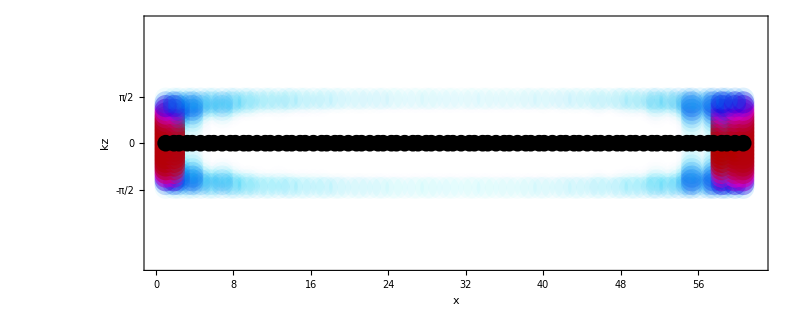

```mathematica
Show[Graphics[{PointSize[0.02],colorfuncOld[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-π-1,π+1}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
FrameTicks->{{{-π/2,0,π/2},None},{Automatic,None}},FrameLabel-> {"x","kz"},
ImageSize-> 800
]
```

```mathematica
(** Rainbow **)
```

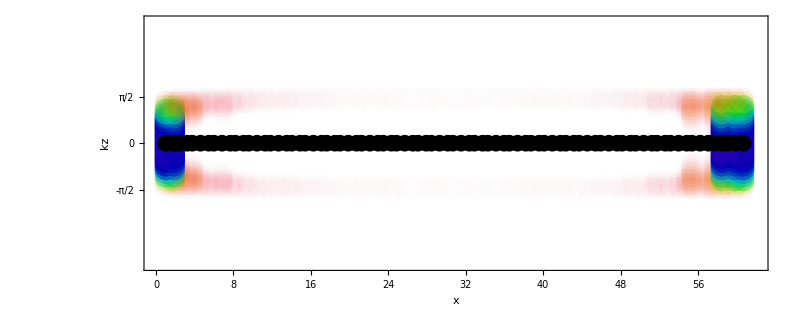

```mathematica
Show[Graphics[{PointSize[0.02],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-π-1,π+1}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
FrameTicks->{{{-π/2,0,π/2},None},{Automatic,None}},FrameLabel-> {"x","kz"},
ImageSize-> 800
]
```

```mathematica
(** Mono color blue **)
```

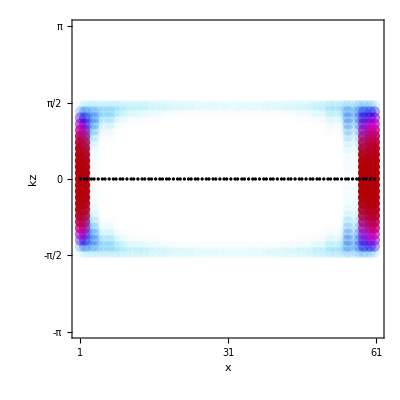

```mathematica
Show[Graphics[{PointSize[0.02],colorfuncOld[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.5,largestX+0.4},{-π,π}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.006]}],
FrameTicks->{{{-π,-π/2,0,π/2,π},None},{{1,31,61},None}},FrameLabel-> {"x","kz"},
ImageSize-> 400,AspectRatio->1
]
```